```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/naomi/Dropbox/&Projects/Small codes

## x and z errors with probability p, planar, mwpm

## store data

```mathematica
convertMWPMdata[data_]:=Sort[{1-(1-#[[3]])^2,1-#[[1]]/#[[2]]}&/@data]
```

```mathematica
convertMWPMdata[s1]>>"data/mwpmS1"
convertMWPMdata[s2]>>"data/mwpmS2"
convertMWPMdata[s3]>>"data/mwpmS3"
convertMWPMdata[s4]>>"data/mwpmS4"
convertMWPMdata[s20]>>"data/mwpmS20"
```

## Plots

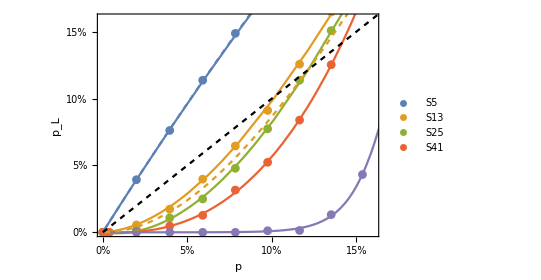

```mathematica
(* import mwpm results *)
mwpmS1=<<"data/mwpmS1";
mwpmS2=<<"data/mwpmS2";
mwpmS3=<<"data/mwpmS3";
mwpmS4=<<"data/mwpmS4";

(* import exact decoder results *)
dataXZP5=<<"data/XZP5";
dataXZP13=<<"data/XZP13";
pLog[data_]:={#[[1]],1-#[[2]]}&/@data;

(* fits to mwpm data *)
fitCubic = a x + b x^2 + c x^3;
fitLogistic = a/(1+Exp[-b(x-c)]);
plots=(fitCubic/.FindFit[#,fitCubic,{a,b,c},x])&/@{mwpmS1,mwpmS2,mwpmS3,mwpmS4[[1;;8]]};
plots=Append[plots,fitLogistic/.FindFit[convertMWPMdata[s20],fitLogistic,{a,b,c},x]];

(* make plots*)
Show[
ListPlot[convertMWPMdata[#]&/@{s1,s2,s3,s4,s20},Joined->False,PlotLegends->{"S5","S13","S25","S41"},PlotMarkers->{"•", 9}],

Plot[plots,{x,0,1}],

ListPlot[pLog@#[[1]],Joined->True,PlotStyle->Directive[Dashing[0.01],ColorData[97,#[[2]]]]]&/@
{{dataXZP5,1},{dataXZP13,2}},

Plot[p,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0,0.16}},
FrameLabel->{"p","p_L"},
LabelStyle->20,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"},{0.2,"20%"}},{},{}},
AspectRatio->0.7
]
```

## raw data

```mathematica
s1={{1,1,0},{48034,50000,0.01},{46193,50000,0.02},{44317,50000,0.03},{85127,100000,0.04},{82122,100000,0.05},{39444,50000,0.06},{37838,50000,0.07},{36397,50000,0.08},{34897,50000,0.09},{33617,50000,0.1}};
s2={{1,1,0},{19890,20000,0.01},{19653,20000,0.02},{19205,20000,0.03},{18709,20000,0.04},{18178,20000,0.05},{17486,20000,0.06},{16706,20000,0.07},{16021,20000,0.08},{15091,20000,0.09},{14459,20000,0.1},{13724,20000,0.11},{13013,20000,0.12},{12380,20000,0.13},{5810,10000,0.14},{5478,10000,0.15},{5256,10000,0.16}};
s3={{1,1,0},{19960,20000,0.01},{19784,20000,0.02},{19501,20000,0.03},{19043,20000,0.04},{18453,20000,0.05},{17726,20000,0.06},{16984,20000,0.07},{16173,20000,0.08},{15382,20000,0.09},{14326,20000,0.1}};
s4={{1,1,0.001},{1,1,0.002},{1,1,0},{19991,20000,0.01},{19905,20000,0.02},{19746,20000,0.03},{19368,20000,0.04},{18953,20000,0.05},{18322,20000,0.06},{17494,20000,0.07},{16581,20000,0.08},{15729,20000,0.09},{14610,20000,0.1}};
s20={{5000,5000,0.01},{5000,5000,0.02},{5000,5000,0.03},{5000,5000,0.04},{4994,5000,0.05},{4993,5000,0.06},{4934,5000,0.07},{4784,5000,0.08},{4405,5000,0.09}};
```